```mathematica
singlePass = {{.5,10*10^-6},{1,20*10^-6},{1.5,31*10^-6},{2,50*10^-6},{2.5,67*10^-6},{3,87*10^-6},{3.5,117*10^-6},{4,144*10^-6},{4.5,177*10^-6},{5,215*10^-6},{5.5,245*10^-6},{6,287*10^-6},{6.5,322*10^-6},{7,370*10^-6}};
```

```mathematica
line = Fit[singlePass,{1,x,x^2},x]
```

-5.93407×10^-7+0.00001395 x+5.58791×10^-6 x^2

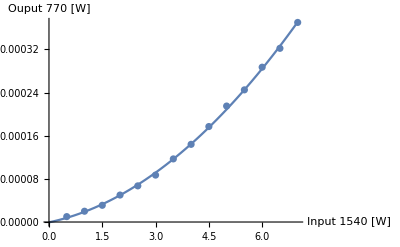

```mathematica
Show[ListPlot[singlePass],Plot[-5.934065934066527*^-7+0.000013950000000000007 x+5.587912087912086*^-6 x^2,{x,0,7}],AxesLabel->{"Input 1540 [W]","Ouput 770 [W]"}]
```

2020.01.17. The conversion efficiency is highly dependent on the crystal temperature and should be varied +- 4 C or so. Here is the single pass data today for T = 79.01 C.

```mathematica
pin = {.5,1,1.5,2,2.5,3,3.7,4.2,4.7,5.2,5.7,6.2,6.7,7.2};
pout = {20.3,80,180,323,506,730,1100,1400,1835,2150,2650,3060,3650,4300}*10^-6;
```

```mathematica
singlePass = Transpose@{pin,pout};
```

```mathematica
line[x_] = Fit[singlePass,{1,x,x^2},x]
```

0.0000247715-0.0000242304 x+0.000084721 x^2

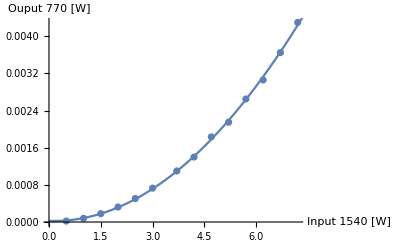

```mathematica
Show[ListPlot[singlePass],Plot[line[x],{x,0,7.5}],AxesLabel->{"Input 1540 [W]","Ouput 770 [W]"},PlotLegends->Placed[{{"0.000024771-0.000024230 x+0.000084721 x^2"},None},{0.8,0.8}]]
```

```mathematica
Clear[line]
```